```mathematica
Jx=1.1012*10^9;
Jy=0.35*10^8;
m=8.4*10^16;
G=6.674*10^-11;
μ=G m;

r=√(x^2+y^2+z^2);
Subscript[U, 0]=μ/r;
Subscript[U, 2]=-1/2 μ/r^3(Jx+Jy)+3/2 μ/r^5(x^2 Jx+y^2 Jy);
Subscript[U, 4]=45/56 μ/r^5(Jx^2+Jy^2+2/3 Jx Jy)-450/56 μ/r^7(x^2(Jx^2+1/3 Jx Jy)+y^2(Jy^2+1/3 Jx Jy))+525/56 μ/r^9(x^4 Jx^2+y^4 Jy^2+2 x^2 y^2 Jx Jy);
```

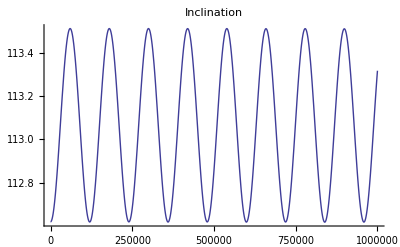

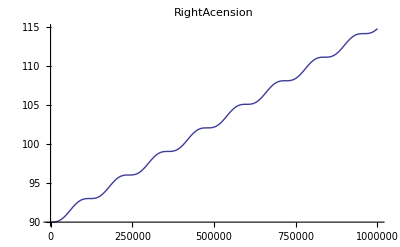

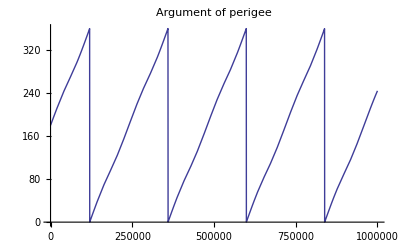

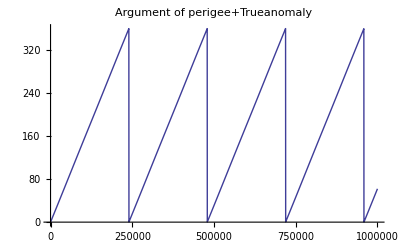

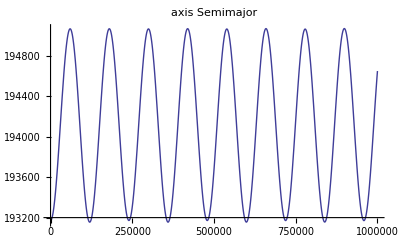

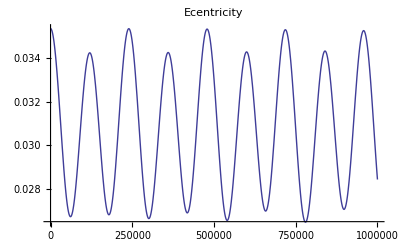

```mathematica
R[t_]:=If[coordinaterotaion==0,{p[t],q[t],w[t]},{Cos[ω t]p[t]-Sin[ω t]q[t],Sin[ω t]p[t]+Cos[ω t]q[t],w[t]}]
V[t_]:=R'[t]
d[t_]:=Norm[R[t]]
v[t_]:=Norm[V[t]]
H[t_]:=R[t]×V[t]
h[t_]:=Norm[H[t]]
incle[t_]:=ArcCos[(H[t][[3]])/h[t]]
Na[t_]:={0,0,1}×H[t]
n[t_]:=Norm[Na[t]]
RA[t_]:=If[n[t]≠0,If[Na[t][[2]]≥0,ArcCos[Na[t][[1]]/n[t]],2π-ArcCos[Na[t][[1]]/n[t]]],0];
Ec[t_]:=1/μ((v[t]^2-μ/d[t])R[t]-(R[t].V[t])V[t]);
ec[t_]:=Norm[Ec[t]];
a[t_]:=h[t]^2/(μ(1-ec[t]^2))
ωp[t_]:=If[Ec[t][[3]]>=0,ArcCos[(Na[t].Ec[t])/(n[t]ec[t])],2π-ArcCos[(Na[t].Ec[t])/(n[t]ec[t])]]
u[t_]:=If[R[t][[3]]>=0,ArcCos[(Na[t].R[t])/(n[t]d[t])],2π-ArcCos[(Na[t].R[t])/(n[t]d[t])]]
Plot[incle[t]/°,{t,0,dur},PlotLabel->Inclination]
Plot[RA[t]/°,{t,0,dur},PlotLabel-> RightAcension]
Plot[ωp[t]/°,{t,0,dur},PlotLabel->Argument of perigee]
Plot[u[t]/°,{t,0,dur},PlotLabel->Argument of perigee+Trueanomaly]
Plot[a[t],{t,0,dur},PlotLabel-> Semimajor axis]
Plot[ec[t],{t,0,dur},PlotLabel->Ecentricity]
```

```mathematica
ω=0.0000259;
coordinaterotaion=0;
dur=2000000;
Subscript[U, x][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]), x];
Subscript[U, y][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]), y];
Subscript[U, z][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]), z];

{p,q,w}=NDSolveValue[{x''[t]==Cos[ω t]Subscript[U, x][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]]-Sin[ω t]Subscript[U, y][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		y''[t]==Sin[ω t]Subscript[U, x][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]]+Cos[ω t]Subscript[U, y][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		z''[t]==Subscript[U, z][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		z[0]==0,y[0]==200000,x[0]==0,x'[0]==0*200000*ω,z'[0]==5.3,y'[0]==0},{x,y,z},{t,dur},MaxSteps->10000000];

orbitgcrf=ParametricPlot3D[{p[t],q[t],w[t]},{t,0,dur}];
orbititrf=ParametricPlot3D[{Cos[ω t]p[t]+Sin[ω t]q[t],-Sin[ω t]p[t]+Cos[ω t]q[t],w[t]},{t,0,dur}];
body=ParametricPlot3D[{106000Cos[u] Sin[v],24000 Sin[u] Sin[v],15000Cos[v]},{u,0,2 π},{v,-π,π}];
Show[orbitgcrf,body]
Show[orbititrf,body]
```

-Graphics3D-

-Graphics3D-

```mathematica
ω=0.0000297196;
coordinaterotaion=0;
dur=1000000;

Subscript[U, x][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), x];
Subscript[U, y][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), y];
Subscript[U, z][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), z];

{p,q,w}=NDSolveValue[{
		x''[t]==Cos[ω t]Subscript[U, x][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]]-Sin[ω t]Subscript[U, y][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		y''[t]==Sin[ω t]Subscript[U, x][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]]+Cos[ω t]Subscript[U, y][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		z''[t]==Subscript[U, z][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		z[0]==0,y[0]==0,x[0]==200000,x'[0]==0,z'[0]==0,y'[0]==5.369757},{x,y,z},{t,dur},MaxSteps->10000000];

orbitgcrf=ParametricPlot3D[{p[t],q[t],w[t]},{t,0,dur}];
orbititrf=ParametricPlot3D[{Cos[ω t]p[t]+Sin[ω t]q[t],-Sin[ω t]p[t]+Cos[ω t]q[t],w[t]},{t,0,dur}];
body=ParametricPlot3D[{106000Cos[u] Sin[v],24000 Sin[u] Sin[v],15000Cos[v]},{u,0,2 π},{v,-π,π}];
Show[orbitgcrf,body]
Show[orbititrf,body]
```

-Graphics3D-

-Graphics3D-

```mathematica
ω=0.00003;
coordinaterotaion=0;
dur=30000000;

Subscript[U, x][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), x];
Subscript[U, y][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), y];
Subscript[U, z][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), z];

{p,q,w}=NDSolveValue[{
		x''[t]==Cos[ω t]Subscript[U, x][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]]-Sin[ω t]Subscript[U, y][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		y''[t]==Sin[ω t]Subscript[U, x][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]]+Cos[ω t]Subscript[U, y][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		z''[t]==Subscript[U, z][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		z[0]==0,y[0]==200000,x[0]==0,x'[0]==0,z'[0]==5.4,y'[0]==0},{x,y,z},{t,dur},MaxSteps->10000000];

orbitgcrf=ParametricPlot3D[{p[t],q[t],w[t]},{t,0,dur}];
orbititrf=ParametricPlot3D[{Cos[ω t]p[t]+Sin[ω t]q[t],-Sin[ω t]p[t]+Cos[ω t]q[t],w[t]},{t,0,dur}];
body=ParametricPlot3D[{106000Cos[u] Sin[v],24000 Sin[u] Sin[v],15000Cos[v]},{u,0,2 π},{v,-π,π}];
Show[orbitgcrf,body]
Show[orbititrf,body]
```

-Graphics3D-

-Graphics3D-

```mathematica
ω=0.004;
coordinaterotaion=0;
dur=10000000;

Subscript[U, x][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), x];
Subscript[U, y][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), y];
Subscript[U, z][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), z];

{p,q,w}=NDSolveValue[{
		x''[t]==Cos[ω t]Subscript[U, x][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]]-Sin[ω t]Subscript[U, y][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		y''[t]==Sin[ω t]Subscript[U, x][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]]+Cos[ω t]Subscript[U, y][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		z''[t]==Subscript[U, z][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		z[0]==0,y[0]==150000,x[0]==0,x'[0]==3,z'[0]==5.4,y'[0]==0},{x,y,z},{t,dur},MaxSteps->10000000];

orbitgcrf=ParametricPlot3D[{p[t],q[t],w[t]},{t,0,dur}];
orbititrf=ParametricPlot3D[{Cos[ω t]p[t]+Sin[ω t]q[t],-Sin[ω t]p[t]+Cos[ω t]q[t],w[t]},{t,0,dur}];
body=ParametricPlot3D[{106000Cos[u] Sin[v],24000 Sin[u] Sin[v],15000Cos[v]},{u,0,2 π},{v,-π,π}];
Show[orbitgcrf,body]
Show[orbititrf,body]
```

-Graphics3D-

-Graphics3D-

```mathematica
ω=0.00000044;
coordinaterotaion=1;
dur=1000000;
Subscript[U, x][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]), x];
Subscript[U, y][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]), y];
Subscript[U, z][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]), z];

{p,q,w}=NDSolveValue[{x''[t]-2ω y'[t]-ω^2 x[t]==Subscript[U, x][x[t],y[t],z[t]],
		y''[t]+2ω x'[t]-ω^2 y[t]==Subscript[U, y][x[t],y[t],z[t]],
		z''[t]==Subscript[U, z][x[t],y[t],z[t]],
		z[0]==0,y[0]==200000,x[0]==0,x'[0]==2.088,z'[0]==4.8,y'[0]==0},{x,y,z},{t,dur},MaxSteps->10000000];

Plot[(2ω q'[t]+ω^2 p[t])+(3 G Jx p[t])/((p[t]^2+q[t]^2+w[t]^2)^(5/2)),{t,0,dur}];
Plot[(-2ω p'[t]+ω^2 q[t])+(3 G Jy q[t])/((p[t]^2+q[t]^2+w[t]^2)^(5/2)),{t,0,dur}];
Plot[(G m p[t])/((p[t]^2+q[t]^2+w[t]^2)^(3/2)),{t,0,dur}];

orbitgcrf=ParametricPlot3D[{Cos[ω t]p[t]-Sin[ω t]q[t],Sin[ω t]p[t]+Cos[ω t]q[t],w[t]},{t,0,dur}];
orbititrf=ParametricPlot3D[{p[t],q[t],w[t]},{t,0,dur}];
body=ParametricPlot3D[{106000Cos[u] Sin[v],24000 Sin[u] Sin[v],15000Cos[v]},{u,0,2 π},{v,-π,π}];
Show[orbitgcrf,body]
Show[orbititrf,body]
```

-Graphics3D-

-Graphics3D-

```mathematica
ω=0.0000003;
coordinaterotaion=0;
dur=10000000;

Subscript[U, x][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), x];
Subscript[U, y][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), y];
Subscript[U, z][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), z];

{p,q,w}=NDSolveValue[{
		x''[t]==Cos[ω t]Subscript[U, x][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]]-Sin[ω t]Subscript[U, y][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		y''[t]==Sin[ω t]Subscript[U, x][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]]+Cos[ω t]Subscript[U, y][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		z''[t]==Subscript[U, z][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		z[0]==0,y[0]==200000,x[0]==0,x'[0]==0,z'[0]==5.2,y'[0]==0},{x,y,z},{t,dur},MaxSteps->10000000];

orbitgcrf=ParametricPlot3D[{p[t],q[t],w[t]},{t,0,dur}];
orbititrf=ParametricPlot3D[{Cos[ω t]p[t]+Sin[ω t]q[t],-Sin[ω t]p[t]+Cos[ω t]q[t],w[t]},{t,0,dur}];
body=ParametricPlot3D[{106000Cos[u] Sin[v],24000 Sin[u] Sin[v],15000Cos[v]},{u,0,2 π},{v,-π,π}];
Show[orbitgcrf,body]
Show[orbititrf,body]
```

-Graphics3D-

-Graphics3D-

```mathematica
ω=0.00002678;
coordinaterotaion=0;
dur=10000000;
Subscript[U, x][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), x];
Subscript[U, y][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), y];
Subscript[U, z][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), z];

{p,q,w}=NDSolveValue[{
		x''[t]==Cos[ω t]Subscript[U, x][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]]-Sin[ω t]Subscript[U, y][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		y''[t]==Sin[ω t]Subscript[U, x][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]]+Cos[ω t]Subscript[U, y][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		z''[t]==Subscript[U, z][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		z[0]==0,y[0]==200000,x[0]==0,x'[0]==-5.18,z'[0]==0.05,y'[0]==0},{x,y,z},{t,dur},MaxSteps->10000000];

orbitgcrf=ParametricPlot3D[{p[t],q[t],w[t]},{t,0,dur}];
orbititrf=ParametricPlot3D[{Cos[ω t]p[t]+Sin[ω t]q[t],-Sin[ω t]p[t]+Cos[ω t]q[t],w[t]},{t,0,dur}];
body=ParametricPlot3D[{106000Cos[u] Sin[v],24000 Sin[u] Sin[v],15000Cos[v]},{u,0,2 π},{v,-π,π}];
Show[orbitgcrf,body]
Show[orbititrf,body]
```

-Graphics3D-

-Graphics3D-

```mathematica
ω=0.00005;
coordinaterotaion=0;
dur=10000000;
Subscript[U, x][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), x];
Subscript[U, y][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), y];
Subscript[U, z][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), z];

{p,q,w}=NDSolveValue[{
		x''[t]==Cos[ω t]Subscript[U, x][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]]-Sin[ω t]Subscript[U, y][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		y''[t]==Sin[ω t]Subscript[U, x][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]]+Cos[ω t]Subscript[U, y][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		z''[t]==Subscript[U, z][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		z[0]==0,y[0]==150000,x[0]==0,x'[0]==6.5,z'[0]==1,y'[0]==0},{x,y,z},{t,dur},MaxSteps->10000000];
orbitgcrf=ParametricPlot3D[{p[t],q[t],w[t]},{t,0,dur}];
orbititrf=ParametricPlot3D[{Cos[ω t]p[t]+Sin[ω t]q[t],-Sin[ω t]p[t]+Cos[ω t]q[t],w[t]},{t,0,dur}];
body=ParametricPlot3D[{106000Cos[u] Sin[v],24000 Sin[u] Sin[v],15000Cos[v]},{u,0,2 π},{v,-π,π}];
Show[orbitgcrf,body]
Show[orbititrf,body]
```

-Graphics3D-

-Graphics3D-

```mathematica
ω=0;
coordinaterotaion=0;
dur=10000000;
Subscript[U, x][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), x];
Subscript[U, y][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), y];
Subscript[U, z][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), z];

{p,q,w}=NDSolveValue[{
		x''[t]==Cos[ω t]Subscript[U, x][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]]-Sin[ω t]Subscript[U, y][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		y''[t]==Sin[ω t]Subscript[U, x][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]]+Cos[ω t]Subscript[U, y][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		z''[t]==Subscript[U, z][Cos[ω t]x[t]+Sin[ω t]y[t],-Sin[ω t]x[t]+Cos[ω t]y[t],z[t]],
		z[0]==0,y[0]==100000,x[0]==0,x'[0]==5,z'[0]==7,y'[0]==0},{x,y,z},{t,dur},MaxSteps->10000000];
orbitgcrf=ParametricPlot3D[{p[t],q[t],w[t]},{t,0,dur}];
orbititrf=ParametricPlot3D[{Cos[ω t]p[t]+Sin[ω t]q[t],-Sin[ω t]p[t]+Cos[ω t]q[t],w[t]},{t,0,dur}];
body=ParametricPlot3D[{106000Cos[u] Sin[v],24000 Sin[u] Sin[v],15000Cos[v]},{u,0,2 π},{v,-π,π}];
Show[orbitgcrf,body]
Show[orbititrf,body]
```

-Graphics3D-

-Graphics3D-

```mathematica
ω=0.00005;
coordinaterotaion=1;
dur=1000000;
Subscript[U, x][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), x];
Subscript[U, y][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), y];
Subscript[U, z][x_,y_,z_]=D[(Subscript[U, 0]+Subscript[U, 2]+Subscript[U, 4]), z];
{p,q,w}=NDSolveValue[{
		x''[t]-2ω y'[t]-ω^2 x[t]==Subscript[U, x][x[t],y[t],z[t]],
		y''[t]+2ω x'[t]-ω^2 y[t]==Subscript[U, y][x[t],y[t],z[t]],
		z''[t]==Subscript[U, z][x[t],y[t],z[t]],
		z[0]==0,y[0]==-127379.127,x[0]==0,x'[0]==0,z'[0]==0,y'[0]==0},{x,y,z},{t,dur},MaxSteps->10000000];

orbitgcrf=ParametricPlot3D[{Cos[ω t]p[t]-Sin[ω t]q[t],Sin[ω t]p[t]+Cos[ω t]q[t],w[t]},{t,0,dur}];
orbititrf=ParametricPlot3D[{p[t],q[t],w[t]},{t,0,dur}];
body=ParametricPlot3D[{106000Cos[u] Sin[v],24000 Sin[u] Sin[v],15000Cos[v]},{u,0,2 π},{v,-π,π}];
Show[orbitgcrf,body]
Show[orbititrf,body]
```

-Graphics3D-

-Graphics3D-